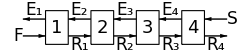

```mathematica
Module[{stages},
stages=4;

Graphics[{
{EdgeForm[Thick],FaceForm[None],Table[Rectangle[{i,0},{i+0.5,1}],{i,1,stages}]},
{Thick,Table[{Arrow[{{i-0.5,0.25},{i,0.25}}],Arrow[{{i,0.75},{i-0.5,0.75}}]},{i,1,stages+1}]},
Table[{Text[Style[i,18],{i+0.25,0.5}],Text[Style[Subscript["E",i],17],{i-0.25,0.75},{0,-1}],Text[Style[Subscript["R",i],17],{i+0.75,0.25},{0,1}]},{i,1,stages}],
Text[Style[" S",17],{stages+1,0.75},{-1,0}],Text[Style["F ",17],{0.5,0.25},{1,0}]
},ImageSize->250]
]
```